```mathematica
base = {FontSize->12,FontFamily->"Times New Roman"};
Unprotect[HeavisideTheta];
HeavisideTheta[0]=1;
HeavisideTheta[0.0]=1;
Protect[HeavisideTheta];

 
addsymbolFxy[list_] := Transpose[{Array[Unique["Fx"]&, Length[list]],Array[Unique["Fy"]&, Length[list]], list}] 
addsymbolFy[list_] := Transpose[{Table[0,Length[list]],Array[Unique["Fy"]&, Length[list]], list}]

igVd[{p_,pos1_,q_,pos2_}][x_]:=(p-(x-pos1)/(pos2-pos1) (p-q))(HeavisideTheta[x-pos1]-HeavisideTheta[x-pos2])
igVfd[{f_,pos1_,pos2_}][x_]:=(HeavisideTheta[x-pos1]-HeavisideTheta[x-pos2])f;
igV[{Fx_,Fy_,pos_}][x_]:=Fy DiracDelta[x-pos]
igMh[{Mh_,pos_}][x_]:=-Mh DiracDelta'[x-pos]
igSc[{Fx_,Fy_,pos_}][x_]:=Fy DiracDelta''[x-pos]

urule[x_, L_] := {HeavisideTheta[(a_)?(NumberQ[N[#/L]] &)] :> HeavisideTheta[Cancel[a/L]], HeavisideTheta[x] :> 1}
evalrep[x_, v_, vp_] := ReplaceAll[v, #] & /@ Thread[x -> Last /@ vp] 

NoDelta := DiracDelta -> (0 &)
takeUnkwnV[{a_,b_,c_}]:=b

NWmax[{V_,M_,S_,w_,L_,x_}]:= NMaximize[{Abs[w],0<x<L},x]
Deflection[{V_,M_,S_,w_,L_,x_},a_]:=Simplify[w/.x->a,Assumptions->{a<=L,L>0,0<=x<=L}]

Options[Beam] = {PointLoad -> {}, LineLoad -> {},LoadFunction->{}, MomentLoad -> {}, InterPin->{}, InterRoller->{}, ShearConnection->{}};

BeamConfig[x_Symbol, L_, IE_, bnd:{_String, _String}, options___Rule] := Module[
{pointLoad,lineLoad,loadFunction,momentLoad,interPin,interRoller,shearcon}, 
{pointLoad , lineLoad ,loadFunction,  momentLoad,interPin,interRoller,shearcon} =First/@Options[Beam]/.parameters[Beam,options]/.Options[Beam];
<|
"pointLoad"->pointLoad,
"lineLoad"->lineLoad,
"loadFunction"->loadFunction,
"momentLoad"->momentLoad,
"interPin"->interPin,
"interRoller"->interRoller,
"shearcon"-> shearcon,
"x"->x,
"L"->L,
"IE"->IE,
"bnd"->bnd
|>]

Beam[beamConfig_] := Module[
{pointLoad,lineLoad,loadFunction,momentLoad,interPin,interRoller,shearcon,q,V,M,S,w,nullLoadL,nullLoadR,bndL,bndR,boundaryCondParts,eqns,soln,res,c1,c2,c3,c4,x,L,IE,bnd}, 
	pointLoad=beamConfig["pointLoad"];
	lineLoad=beamConfig["lineLoad"];
	loadFunction=beamConfig["loadFunction"];
	momentLoad=beamConfig["momentLoad"];
	interPin=beamConfig["interPin"];
	interRoller=beamConfig["interRoller"];
	shearcon=beamConfig["shearcon"];
	x=beamConfig["x"];
	L=beamConfig["L"];
	IE=beamConfig["IE"];
	bnd=beamConfig["bnd"];

{interPin,shearcon} =addsymbolFxy/@{interPin,shearcon}; 
{interRoller} =addsymbolFy/@{interRoller};

q = Join[
	Map[igV[#][x]&,DeleteCases[Join[Partition[pointLoad,3],interPin,interRoller],{_,_,0|0.0}|{_,_,L}]],
	Map[igVd[#][x]&,Partition[lineLoad,4]],
	Map[igVfd[#][x]&,Partition[loadFunction,3]],
	Map[igMh[#][x]&,DeleteCases[Partition[momentLoad,2],{_,0|0.0}|{_,L}]],
	Map[igSc[#][x]&,shearcon]
	];
V = Append[Integrate[q,x],c1];
M = Append[Integrate[-V,x],c2];
S = Append[Integrate[-M/IE,x],c3]/.urule[x,L];
w = Append[Integrate[S,x],c4];

nullLoadL = Join[{Cases[Partition[pointLoad, 3], {_,_, 0 | 0.0}]/.{{{_,P_, _}} :> -P, {} :> 0}}, {Cases[Partition[momentLoad, 2], {_, 0 | 0.0}]/.{{{P_, _}} :> -P, {} :> 0}}] ;
bndL = Switch[ First[bnd], "Fixed", {w, S}, "Pinned", {w, Append[M, Last[nullLoadL]]},
     "Free",  {Append[M, Last[nullLoadL]], Append[V, First[nullLoadL]]}, "Roller", {w, Append[M, Last[nullLoadL]]}] /. x -> 0;

nullLoadR = Join[{Cases[Partition[pointLoad, 3], {_,_, L }]/.{{{_,P_, _}} :> P, {} :> 0}}, {Cases[Partition[momentLoad, 2], {_,L}]/.{{{P_, _}} :> P, {} :> 0}}] ;
bndR= Switch[ Last[bnd], "Fixed", {w, S}, "Pinned", {w, Append[M, Last[nullLoadR]]},
     "Free",  {Append[M, Last[nullLoadR]], Append[V, First[nullLoadR]]}, "Roller", {w, Append[M, Last[nullLoadR]]}] /. x -> L;
boundaryCondParts = Join[bndR, bndL, evalrep[x, w, interPin], evalrep[x, w, interRoller], evalrep[x, M, shearcon]];
eqns = Thread[ Apply[Plus, boundaryCondParts, 1] == 0 ] /.NoDelta /.urule[x,L];
soln =  Flatten@Solve[eqns, Join[ {c1, c2, c3, c4}, takeUnkwnV/@ Join[interPin,interRoller, shearcon]]]; 
res = Join[Simplify[Apply[Plus, {V, M, S, w} /. NoDelta/.urule[x,L] /. soln,1 ],Assumptions->{0<=x<L}] ,{L},{x}](*V(x), Mh(x), φ(x), w(x), L, x *)
]

DiagramsPlot[{V_,M_,S_,w_,L_,x_}]:=Module[
{VPlot,MPlot,SPlot,wPlot},
VPlot=Plot[V,{x,0,L},ImageSize -> 350,PlotLabel->"Nyíróerő ábra",PlotStyle->Blue,AspectRatio->0.4,Filling->Axis,BaseStyle->base,PlotRange->All,AxesOrigin->{0,0},LabelStyle->Black,GridLines->Automatic,AxesLabel->{Row[{Style["x",FontSlant->Italic]," (m)"}],Row[{Style["V",FontSlant->Italic]," (N)"}]}];
MPlot=Plot[M,{x,0,L},ImageSize -> 350,PlotLabel->"Hajlítónyomatéki ábra",PlotStyle->Red,AspectRatio->0.4,Filling->Axis,BaseStyle->base,PlotRange->All,AxesOrigin->{0,0}, LabelStyle->Black,GridLines->Automatic,AxesLabel->{Row[{Style["x",FontSlant->Italic]," (m)"}],Row[{Style["\!\(\*SubscriptBox[\(M\), \(h\)]\)",FontSlant->Italic]," (Nm)"}]}];
SPlot=Plot[S,{x,0,L},ImageSize -> 350,PlotLabel->"Szögelfordulás ábra",PlotStyle->Green,AspectRatio->0.4,Filling->Axis,BaseStyle->base,PlotRange->All,LabelStyle->Black,GridLines->Automatic,AxesLabel->{Row[{Style["x",FontSlant->Italic]," (m)"}],Row[{Style["S",FontSlant->Italic]," (rad)"}]}];
wPlot=Plot[w,{x,0,L},ImageSize -> 350,PlotLabel->"Lehajlás ábra",PlotStyle->Brown,AspectRatio->0.4,Filling->Axis,BaseStyle->base,PlotRange->All,LabelStyle->Black,GridLines->Automatic,AxesLabel->{Row[{Style["x",FontSlant->Italic]," (m)"}],Row[{Style["w",FontSlant->Italic]," (m)"}]}];
Column[{VPlot, MPlot, SPlot, wPlot}]
]

ReactionForce[{V_,M_,S_,w_,L_,x_},a_]:= Module[{vValos},
vValos = Piecewise[{{V,0<x<L},{0,True}}];
Simplify[Limit[vValos,x->a,Direction->"FromAbove"]-Limit[vValos,x->a,Direction->"FromBelow"],Assumptions->{a<=L,L>0,0<=x<=L}]
]

ReactionMoment[{V_,M_,S_,w_,L_,x_},a_]:=Module[{MValos},
MValos = Piecewise[{{M,0<x<L},{0,True}}];
Simplify[Limit[MValos,x->a,Direction->"FromAbove"]-Limit[MValos,x->a,Direction->"FromBelow"],Assumptions->{a<=L,L>0,0<=x<=L}]
]

parameters[name_,options___Rule] :=FilterRules[{options},Options[name]];

DrawBeam[beamConfig_]:=Module[{length = beamConfig["L"], varsToClear = {},pointLoad = beamConfig["pointLoad"],lineLoad = beamConfig["lineLoad"], momentLoad = beamConfig["momentLoad"], canvasWidth, canvasHeight,pins,scale,paddingx,paddingy,arrows,beam,pinToDraw,Fynom,Fymax,arrowsNormed,pointLoadToDraw,toDraw,shearcons, shearconsToDraw,fixedSupportsToDraw,lineLoads,p0nom,p0max,lineLoadsNormed,lineLoadsToDraw,coordinateAxes,DrawPin,DrawArrow,NormSublist,NormLineLoads, DrawFixedSupportLeft,DrawFixedSupportRight,  DrawLineLoad,DrawMoment,momentLoads,momentToDraw,NormLoadFunc,DrawLoadFunction,loadFunctions,getMax,fpmax,loadFunctionsNormed,loadFunctionsToDraw,loadNorm},
canvasWidth = 500; canvasHeight = 200;
scale = 500 / length;
paddingx = 50;
paddingy = 30;

DrawPin[x_]:= Module[{pinDiameter,sideLength},
pinDiameter = 6;sideLength = 15;
Graphics[{EdgeForm[Black],FaceForm[LightGray],Polygon[{{x,0},{x-sideLength,-Sqrt[3]sideLength},{x+sideLength,-Sqrt[3]sideLength}}],
EdgeForm[Black],Gray,Disk[{x,0},pinDiameter]}]];

DrawArrow[{Fx_,Fy_,x_},color_,thickness_]:=
Graphics[{
color,Thickness[thickness],Arrow[{{x-Fx,-Fy},{x,0}}]}];

NormSublist[sublist_,normFactor_,scale_]:=ReplacePart[sublist,{1->sublist[[1]]*normFactor,2->sublist[[2]]*normFactor,3->sublist[[3]]*scale}];

NormLineLoads[sublist_,normFactor_,scale_]:= ReplacePart[sublist,{1->-sublist[[1]]*normFactor,2->sublist[[2]]*scale,3->-sublist[[3]]*normFactor,4->sublist[[4]]*scale}];

NormLoadFunc[sublist_,normFactor_]:=ReplacePart[sublist,{1->-sublist[[1]]*normFactor}] ;

DrawFixedSupportLeft[]:=Module[{height,width},
height = 70; width = 20;
Graphics[{LightGray,Rectangle[{-width,-height/2},{0,height/2}],Thick,Black,Line[{{0,-height/2},{0,height/2}}]}]];

DrawFixedSupportRight[L_]:=Module[{height,width},
height = 70; width = 20;
Graphics[{LightGray,Rectangle[{L,-height/2},{L+width,height/2}],Thick,Black,Line[{{L,-height/2},{L,height/2}}]}]];

DrawLineLoad[{p1_,x1_,p2_,x2_}]:= Graphics[{EdgeForm[Red],FaceForm[RGBColor[1,104/255,98/255,0.4]],Polygon[{{x1,0},{x1,p1},{x2,p2},{x2,0}}]}];
DrawLoadFunction[{func_,xmin_,xmax_},x_]:=Graphics[{EdgeForm[Red],FaceForm[RGBColor[1,104/255,98/255,0.4]],Polygon[Prepend[Append[Table[{x*scale,func},{x,xmin,xmax,(xmax-xmin)/(200)}],{xmax*scale,0}],{xmin*scale,0}]]}];
DrawMoment[{M_,x0_}]:=If[Sign[M]>0,Graphics[{Red,Thickness[0.01],Arrowheads[0.05],Arrow[BSplineCurve[Table[{30Cos[t]+x0,30Sin[t]},{t,-π/3,Pi,Pi/10}]],0.1]}],Graphics[{Red,Thickness[0.01],Arrowheads[{-0.05,0}],Arrow[BSplineCurve[Table[{30Cos[t]+x0,30Sin[t]},{t,-π/3,Pi,Pi/10}]],0.1]}]];

coordinateAxes = Graphics[{Black,Arrowheads[0.035],Arrow[{{-40,0},{canvasWidth+50,0}}],Arrow[{{0,-70},{0,90}}],Style[Text["x",{canvasWidth+35,-15}],FontSlant->"Italic",FontFamily->"Cambria",FontSize->12],Style[Text["y",{-15,80}],FontSlant->"Italic",FontFamily->"Cambria",FontSize->12]}];

beam = Graphics[{Thickness[8/(canvasWidth+2*paddingx)],Black,Line[{{0,0},{length*scale,0}}]}];
pins = beamConfig["interPin"]*scale;
If[First[beamConfig["bnd"]]=="Pinned",AppendTo[pins,0]];
If[Last[beamConfig["bnd"]]=="Pinned",AppendTo[pins,length*scale]];
pinToDraw = Map[DrawPin,pins];

shearcons = beamConfig["shearcon"]*scale;
shearconsToDraw=Graphics[{EdgeForm[Black],Gray,Disk[{#,0},6]}]&/@shearcons;

fixedSupportsToDraw = {};
If[First[beamConfig["bnd"]]== "Fixed",AppendTo[fixedSupportsToDraw,DrawFixedSupportLeft[]]];
If[Last[beamConfig["bnd"]]== "Fixed",AppendTo[fixedSupportsToDraw,DrawFixedSupportRight[length*scale]]];

arrows = Partition[pointLoad,3];
Fynom = 100;
Fymax= Max[Abs[arrows[[All,2]]]];
arrowsNormed = NormSublist[#,Fynom/Fymax,scale]&/@arrows;
pointLoadToDraw=DrawArrow[#,Red,3/(canvasWidth+2paddingx)]&/@arrowsNormed;

lineLoads = Partition[lineLoad,4];
p0nom = 50;
p0max = Max[Abs[Partition[lineLoad,2]][[All,1]]];
loadFunctions = Partition[beamConfig["loadFunction"],3];
getMax[{func_,xmin_,xmax_},var_]:= First[NMaximize[{Abs[func],xmin<=var<=xmax},var]];
fpmax = Max[getMax[#,beamConfig["x"]]&/@loadFunctions];

loadNorm = p0nom/Max[fpmax,p0max];

lineLoadsNormed = NormLineLoads[#,loadNorm,scale]&/@lineLoads;
lineLoadsToDraw = DrawLineLoad[#]&/@lineLoadsNormed;

loadFunctionsNormed = NormLoadFunc[#,loadNorm]&/@loadFunctions;
loadFunctionsToDraw = DrawLoadFunction[#,beamConfig["x"]]&/@loadFunctionsNormed;

momentLoads = Partition[momentLoad,2]*scale;
momentToDraw= Map[DrawMoment,momentLoads];

toDraw = {lineLoadsToDraw,loadFunctionsToDraw,coordinateAxes,beam,pinToDraw,fixedSupportsToDraw,shearconsToDraw,pointLoadToDraw,momentToDraw};
Show[toDraw,PlotRange->{{0-paddingx,canvasWidth+paddingx},{-canvasHeight/2-paddingy,canvasHeight/2+paddingy}}]
]
```

#### Feladatmegoldások

```mathematica
-Graphics-;
```

Paraméteres  megoldás

```mathematica
loadFuncPram = BeamConfig[x,A,IE,{"Fixed","Pinned"},LoadFunction->{-P0 Sin[Pi x/A],0,A},InterPin->{A/3}];
```

```mathematica
solLoadFuncParam = Beam[loadFuncPram];
```

```mathematica
Deflection[solLoadFuncParam,3/4 A](*Paraméteres lehajlás x=3/4 A-ban*)
```

-(A^4 P0 (64 √2-54 √3+5 π))/(128 IE π^4)

```mathematica
ReactionForce[solLoadFuncParam,0] (*Paraméteres reakcióerő x=0-ban*)
```

(A P0 (-1863 √3+756 π+22 π^3))/(22 π^4)

```mathematica
ReactionMoment[solLoadFuncParam,0](*Paraméteres reakció nyomaték x=0-ban*)
```

-(27 A^2 P0 (15 √3-8 π))/(22 π^4)

Numerikus  megoldás

```mathematica
a = 4;p0=500;ie=210 10^9*(0.1^4 π)/64;
```

```mathematica
loadFunc =  BeamConfig[x,a,ie,{"Fixed","Pinned"},LoadFunction->{-p0 Sin[Pi x/a],0,a},InterPin->{a/3}];
```

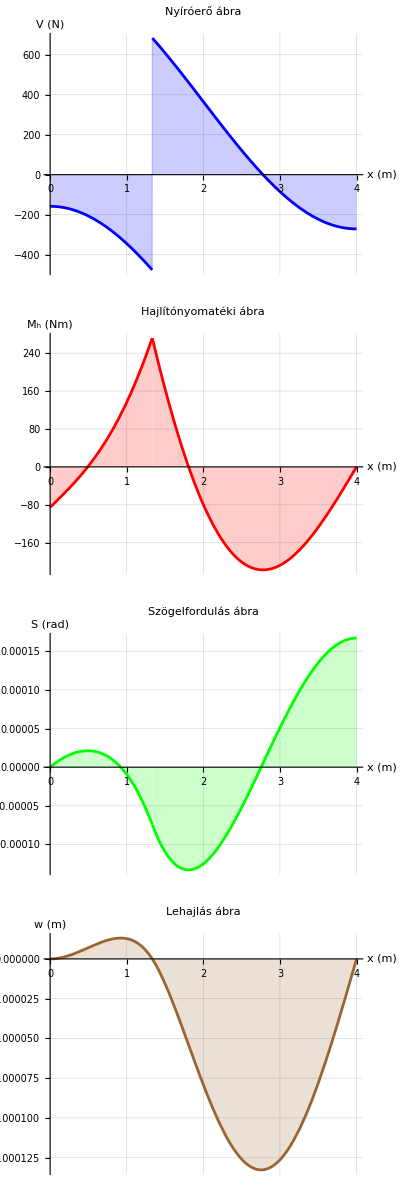

```mathematica
solLoadFunc = Beam[loadFunc];
DiagramsPlot[solLoadFunc]
```

```mathematica
-Graphics-;
```

```mathematica
p0=300;l=1;F=2000;M=3000;IE1=210*10^9*(0.3^4 π)/64;
```

```mathematica
myBeam=BeamConfig[x,10l,IE1,{"Free","Fixed"},InterPin->{4l},PointLoad->{0,-F,0},LineLoad->{p0,l,p0,3l,0,4l,-p0,10l},MomentLoad->{-M,7l}];
```

```mathematica
myBeamSol=Beam[myBeam];
```

```mathematica
DrawBeam[myBeam]
```

-Graphics-

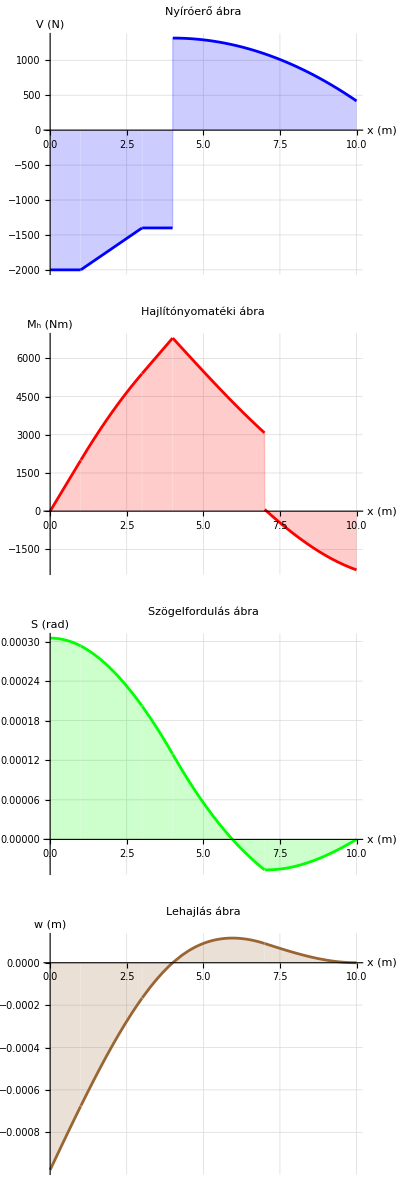

```mathematica
DiagramsPlot[myBeamSol]
```